Práctica 1: Curvas planas

Objetivo: Utilizar Mathematica para definir y dibujar curvas planas, calcular diedros de Frenet y curvaturas, y obtener curvas con curvatura prefijada.

Definición de curvas: Veamos cómo se define en Mathematica una curva parametrizada α(t) con parámetro t.

Ejemplos:

```mathematica
alpha1[t_]:={t^2,t^3};
```

```mathematica
alpha2[t_]:={Cos[t],Sin[3t]};
```

Comandos para la representación gráfica de curvas:

Plot
Plot[f[x], {x, xmin, xmax}] dibuja la gráfica de la función f(x) en la variable x desde xmin hasta xmax. Observa el efecto de los diferentes comandos:



```mathematica
Plot[Sin[t],{t,0,2Pi}]
```

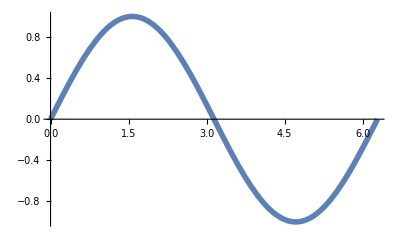

```mathematica
Plot[Sin[t],{t,0,2Pi},PlotStyle->{Thickness[0.01]}]
```

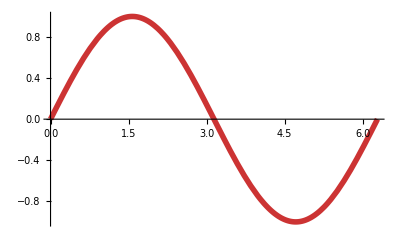

```mathematica
Plot[Sin[t],{t,0,2Pi},PlotStyle->{{Thickness[0.01],
RGBColor[0.8,0.2,0.2]}}]
```

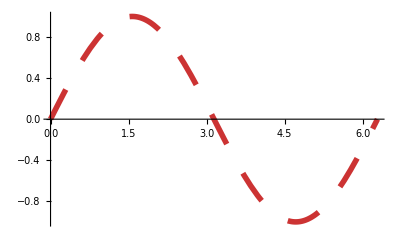

```mathematica
graf1=Plot[Sin[t],{t,0,2Pi},PlotStyle->{{Thickness[0.01],
RGBColor[0.8,0.2,0.2],Dashing[{0.06}]}}]
```

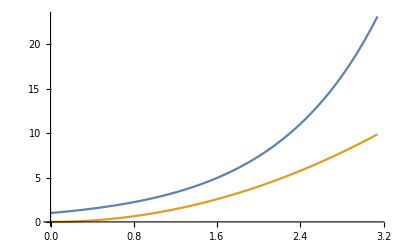

```mathematica
graf2=Plot[{E^t,t^2},{t,0,Pi}]
```

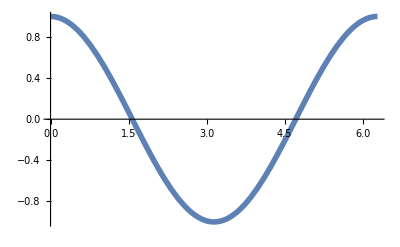

```mathematica
graf3=Plot[Cos[t],{t,0,2Pi},PlotStyle->{Thickness[0.01]}]
```

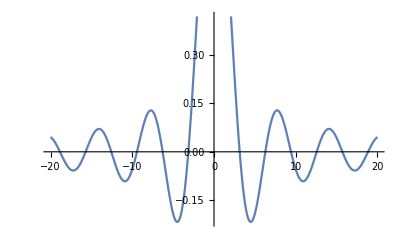

```mathematica
Plot[Sin[t]/t,{t,-20,20}]
```

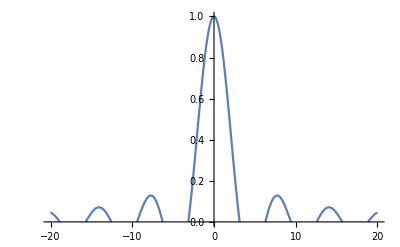

```mathematica
Plot[Sin[t]/t,{t,-20,20},PlotRange->{0,1}]
```

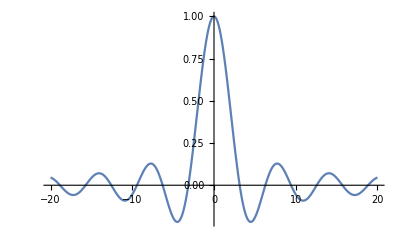

```mathematica
Plot[Sin[t]/t,{t,-20,20},PlotRange->All]
```

Show
Show[graphics, options] muestra uno o varios gráficos usando las opciones especificadas.

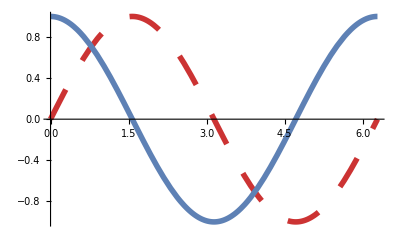

```mathematica
Show[graf1,graf3]
```

ParametricPlot
ParametricPlot[{x[t], y[t]}, {t, tmin, tmax}] dibuja la curva plana α(t)=(x(t),y(t)) en el intervalo [tmin,tmax].

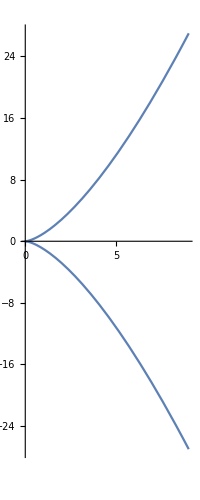

```mathematica
ParametricPlot[alpha1[t]//Evaluate,{t,-3,3}]
```

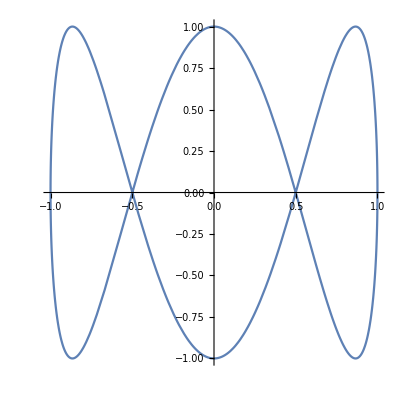

```mathematica
ParametricPlot[alpha2[t]//Evaluate,{t,0,2Pi}]
```



```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]
```

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}, AspectRatio->Automatic]
```

-Graphics-

Ejemplos de curvas planas famosas:

El folium de Descartes.

```mathematica
folium[t_]:={3t/(1+t^3),3t^2/(1+t^3)};
```

Power::infy: Infinite expression 1/0. encountered.

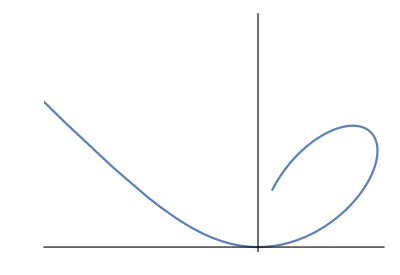

```mathematica
ParametricPlot[folium[t]//Evaluate,{t,-1,4},
AspectRatio->Automatic,Ticks->None,PlotPoints->55]
```

Espiral logarítmica de parámetros a y b.

```mathematica
logspiral[a_,b_][t_]:=E^(a t) {Cos[b t],Sin[b t]};
```

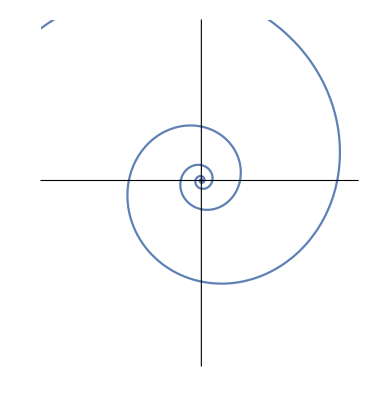

```mathematica
ParametricPlot[logspiral[1,5][t]//Evaluate,{t,-2Pi,2Pi},
AspectRatio->Automatic,Ticks->None,PlotPoints->55]
```

Cicloide de parámetros a y b.

```mathematica
cycloid[a_,b_][t_]:={b Sin[t]-a t,a-b Cos[t]}
```

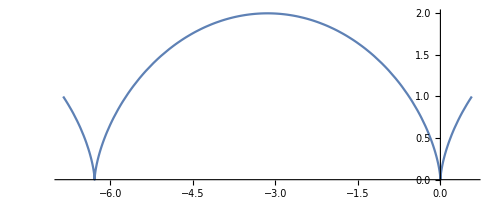

```mathematica
ParametricPlot[cycloid[1,1][t]//Evaluate,{t,-Pi/2,5Pi/2},AspectRatio->Automatic]
```

Lemniscata de Bernouilli de parámetro a. Observa cómo se emplea la orden Table para dibujar varias lemniscatas de parámetro variable.

```mathematica
lemniscate[a_][t_]:={a Cos[t]/(1+Sin[t]^2),a Sin[t] Cos[t]/(1+Sin[t]^2)}
```

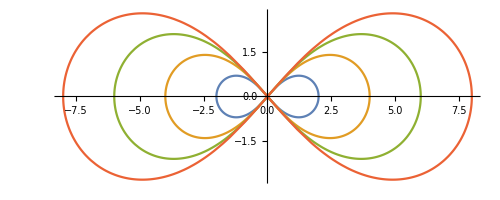

```mathematica
ParametricPlot[Table[lemniscate[a][t],{a,2,8,2}]//Evaluate,{t,0,2Pi},AspectRatio->Automatic]
```

Cardioide de parámetro a. Observa cómo se emplea la orden Table para dibujar varias cardioides de parámetro variable.

```mathematica
cardioid[a_][t_]:={2a Cos[t] (1+Cos[t]),2a Sin[t] (1+Cos[t])}
```

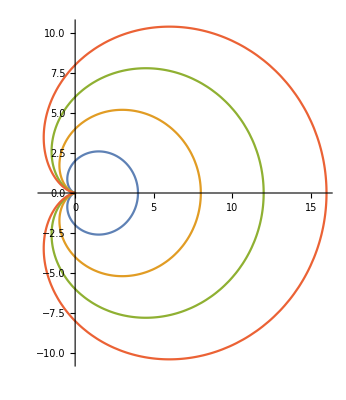

```mathematica
ParametricPlot[Table[cardioid[a][t],{a,1,4,1}]//Evaluate,{t,0,2Pi},
AspectRatio->Automatic]
```

Cisoide de Diocles de parámetro a.

```mathematica
cissoid[a_][t_]:={2a t^2/(1+t^2),2a t^3/(1+t^2)}
```

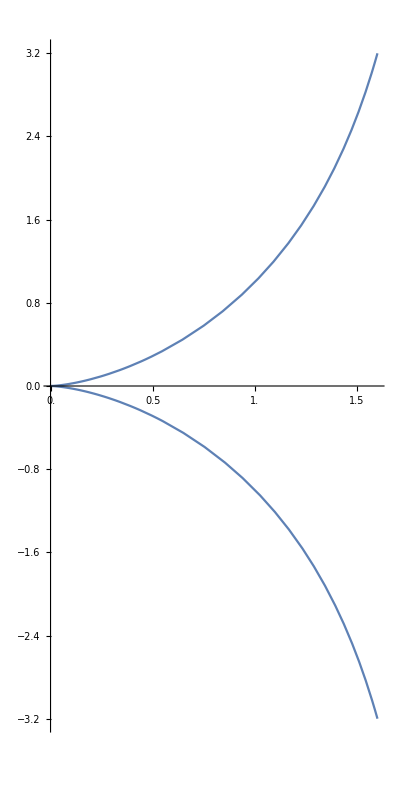

```mathematica
ParametricPlot[cissoid[1][t]//Evaluate,{t,-2,2},AspectRatio->2,Ticks->{Range[0,2,0.5],Automatic},PlotRange->All]
```

Tractriz de parámetro a.

```mathematica
tractrix[a_][t_]:=a{Sin[t],Cos[t]+Log[Tan[t/2]]}
```

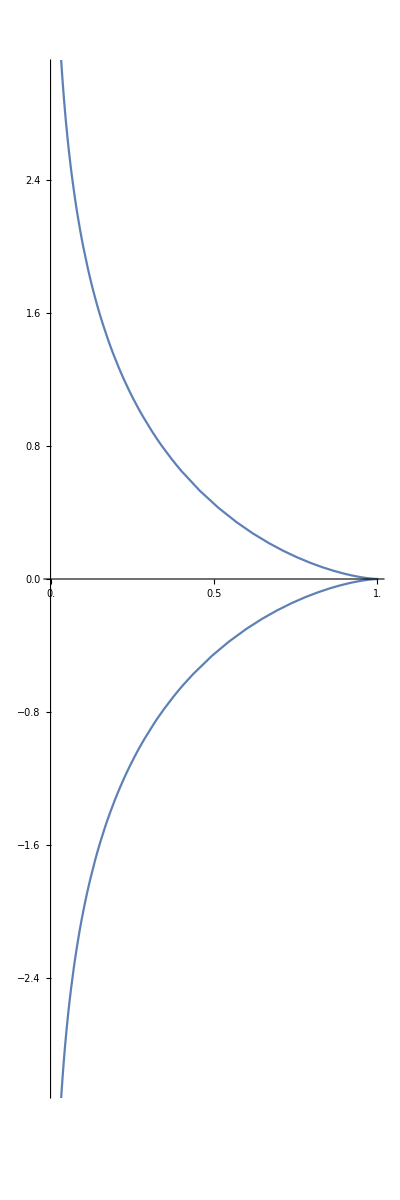

```mathematica
ParametricPlot[tractrix[1][t]//Evaluate,{t,0.01,0.99 Pi},AspectRatio->3,PlotPoints->50,PlotRange->{Automatic,{-3.0,3.0}},Ticks->{Range[0,1,0.5],Automatic}]
```

Ejercicios:

1. Dibuja tres ruedas dentadas (gear curves: ver enlace web número 2 al final de la práctica) practicando los comandos de dibujo anteriores.

```mathematica
r[a_,b_,n_,t_]:=a+1/b*Tanh[b*Sin[n*t]]
```

```mathematica
gearcurve[a_,b_,n_,t_]:={r[a,b,n,t]Cos[t],r[a,b,n,t]Sin[t]}
```

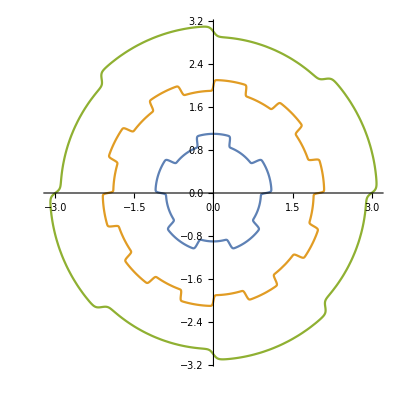

```mathematica
ParametricPlot[{gearcurve[1,10,5,t],gearcurve[2,10,10,t], gearcurve[3,10,4,t]}
//Evaluate,{t,0,2Pi},AspectRatio->Automatic]
```

2. Dibuja una bruja de Agnesi (witch of Agnesi: ver enlace web número 2 al final de la práctica) practicando los comandos de dibujo anteriores.

```mathematica
agnesiwitch[a_,t_]:={2a*Cot[t],a(1-Cos[2t])}
```

```mathematica
ParametricPlot[agnesiwitch[1,t]//Evaluate,{t,-2Pi,2Pi},
AspectRatio->0.5, Ticks->None]
```

-Graphics-

3. Dibuja con diferentes opciones de color y grosor la traza de la curva α(t) = (1-3sen(t)) (cos(t),sen(t)).

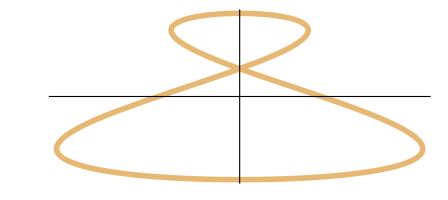
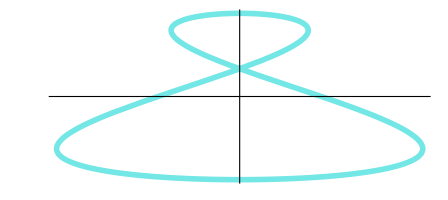
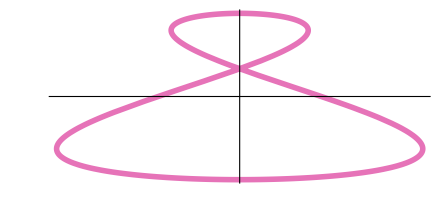

```mathematica
Table[ 
ParametricPlot[{(1-3Sin[t])*Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thickness[.01],Hue[a,0.5,0.9]}, Ticks -> None]
,{a,{0.1,0.5, 0.9}}]
```

Longitud de arco, diedro de Frenet y curvatura de una curva plana:

Longitud del arco de curva comprendido en un intervalo [a,b].

```mathematica
arclengthprime[alpha_][t_]:=Sqrt[Simplify[D[alpha[u],u].
D[alpha[u],u]]] /.u->t
```

```mathematica
arclength[a_,b_][alpha_]:=Integrate[arclengthprime[alpha][t],{t,a,b}];
```

```mathematica
arclength[0,1][alpha1]
```

1/27 (-8+13 √13)

```mathematica
arclength[0,1][alpha2]
```

∫_0^1 √(9 Cos[3 t]^2+Sin[t]^2)ⅆt

```mathematica
N[%]
```

1.96334

Valor numérico de la longitud del arco de curva comprendido en un intervalo [a,b].

```mathematica
lengthn[a_,b_][alpha_]:=NIntegrate[arclengthprime[alpha][t],{t,a,b}]
```

```mathematica
lengthn[0,1][alpha1]
```

1.43971

```mathematica
lengthn[0,1][alpha2]
```

1.96334

Vector tangente de una curva regular plana.

```mathematica
tangent[alpha_][t_]:=D[alpha[u],u]/Simplify[Factor[D[alpha[u],u].D[alpha[u],u]]]^(1/2) /. u->t
```

```mathematica
tangent[alpha1][t]
```

{(2 t)/(√(t^2 (4+9 t^2))),(3 t^2)/(√(t^2 (4+9 t^2)))}

```mathematica
tangent[alpha1][t]//Simplify//PowerExpand
```

{2/(√(4+9 t^2)),(3 t)/(√(4+9 t^2))}

```mathematica
tangent[alpha2][t]
```

{-Sin[t]/(√(9 Cos[3 t]^2+Sin[t]^2)),(3 Cos[3 t])/(√(9 Cos[3 t]^2+Sin[t]^2))}

Vector normal de una curva regular plana.

```mathematica
J:={{0,-1},{1,0}}
```

```mathematica
normal[alpha_][t_]:=J.tangent[alpha][t]
```

```mathematica
normal[alpha1][t]
```

{-(3 t^2)/(√(t^2 (4+9 t^2))),(2 t)/(√(t^2 (4+9 t^2)))}

```mathematica
normal[alpha1][t]//Simplify//PowerExpand
```

{-(3 t)/(√(4+9 t^2)),2/(√(4+9 t^2))}

```mathematica
normal[alpha2][t]//FullSimplify
```

{-(3 Cos[3 t])/(√(9 Cos[3 t]^2+Sin[t]^2)),-Sin[t]/(√(9 Cos[3 t]^2+Sin[t]^2))}

Curvatura de una curva regular plana:

```mathematica
kappa[alpha_][t_]:=
Det[{D[alpha[u],u],D[alpha[u],{u,2}]}]/
Simplify[D[alpha[u],u].D[alpha[u],u]]^(3/2)/.u->t
```

```mathematica
kappa[alpha1][t]//Simplify //PowerExpand
```

6/(t (4+9 t^2)^(3/2))

```mathematica
kappa[alpha2][t]//Simplify
```

(6 Cos[2 t]-3 Cos[4 t])/((9 Cos[3 t]^2+Sin[t]^2)^(3/2))

```mathematica
kappa[logspiral[a,b]][t]//Simplify
```

b/(√((a^2+b^2) ⅇ^(2 a t)))

Ejercicios:

4. Recuerda cómo se define la evoluta de una curva plana (ejercicio 14 de la relación 1). Sea α(t) el grafo de la función cosh(t) y sea β(t) la evoluta de α(t). Representa
sobre un mismo gráfico y con colores distintos las trazas de ambas curvas. Calcula también sus diedros de Frenet y sus curvaturas.
5. Utiliza el ejercicio 3 de la relación 1 para calcular el diedro de Frenet y la curvatura de una elipse. Dibuja también la elipse obtenida para a = 2 y b = 3.

Determinación de una curva plana a partir de su curvatura

Recuerda el enunciado del teorema fundamental para curvas planas. Su demostración se puede implementar en Mathematica para dibujar curvas planas con curvatura prefijada. Para ello utilizaremos comandos de resolución numérica de ecuaciones diferenciales. Veamos un ejemplo:

Curva con curvatura k(s) = s:

```mathematica
k[s_]:=s
```

```mathematica
theta[s_]:=Integrate[k[u],{u,0,s}]
```

```mathematica
curva[s_]:=NDSolve[{x'[s]==Cos[theta[s]],y'[s]==Sin[theta[s]],
x[0]==0,y[0]==0},{x,y},{s,-10,10}];
```

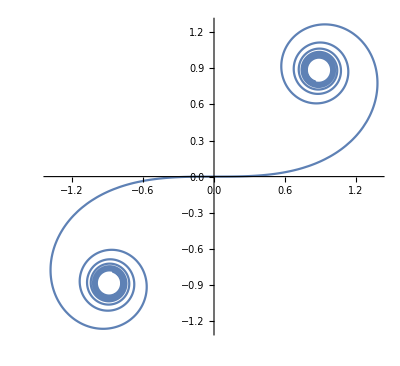

```mathematica
ParametricPlot[Evaluate[{x[s],y[s]}/.curva[s]],{s,-10,10},AspectRatio->Automatic]
```

Ejercicios:

6. Representa la curva plana que tiene por curvatura la función k(s) = -1.
7. Representa la curva plana que tiene por curvatura la función: k(s) = s sen(s).

8. Representa la curva plana que tiene por curvatura la función k(s) = s^2+s.

Algunos enlaces en internet sobre curvas:

1. Índice de curvas famosas:  	www-gap.dcs.st-and.ac.uk/~history/Curves/Curves.html

2. World of Mathematics. Curvas planas:  http://mathworld.wolfram.com/topics/GeneralPlaneCurves.html

3. Curvas chulas en el plano:    http://www.xahlee.org/SpecialPlaneCurves_dir/specialPlaneCurves.html